C:\Users\DANIEL\Desktop\Physics\TESIS\Mathematica

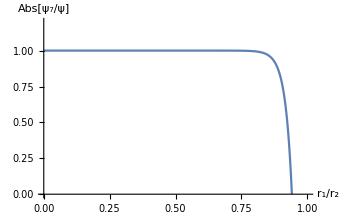

```mathematica
d3[a_,r_,s_,ϵ_,θ_,l_]:=-l (r^(1+2 l)-s^(1+2 l))((1+l) r^(1+2 l) (-1+ϵ)+a^(1+2 l) (1+l+l ϵ)) θ;
Λ[a_,r_,s_,ϵ_,θ_,l_]:=(V*a^(1+l) )/(-l (1+l) r^(2+4 l) (-1+ϵ)^2+a^(1+2 l) (1+l) (r^(1+2 l)-s^(1+2 l)) (-1+ϵ) (1+l+l ϵ)+r^(1+2 l) s^(1+2 l) (1+l+l ϵ) (l+ϵ+l ϵ));
V=3/299.792458;
r2=1;
r=.;
θ=.;


SetDirectory[NotebookDirectory[]]
ticksv[min_,max_]:=Table[{i,Style[i,12],{.02,0},Directive[Black,Thick]},{i,0+0.2,max,0.2}]

ticksh[min_,max_]:=Table[{i,Style[i,12],{.02,0},Directive[Black,Thick]},{i,0+0.1,max,0.1}]
ψ3[a_,r_,θ_,n_]:=
Simplify[Sum[(-1/2)^((l-1)/2)(2l+1)(l-2)!!/(2((l+1)/2)!)*Λ[a,a,r2,4,1/137,l]*(d3[a,a,r2,4,1/137,l]*r^(-l-1))*LegendreP[l,Cos[θ]],{l,1,2*n+1}]-Sum[(-1/2)^((2l-1)/2)(4l+1)(2l-2)!!/(2((2l+1)/2)!)*Λ[a,a,r2,4,1/137,2l]*(d3[a,a,r2,4,1/137,2l]*r^(-2l-1))*LegendreP[2l,Cos[θ]],{l,1,n}]];

Plot[ψ3[a*r2,r2,0,11]/ψ3[a*r2,r2,0,150],{a,0,1},PlotRange->{0,1.2},AxesLabel->{Style[Subscript[r,1]/Subscript[r,2],12],Style[Abs[Subscript[ψ,7]/ψ],12]},AxesStyle->Black,ImageSize->350]
Export["approx.png",plot,ImageResolution->600]
```

C:\Users\DANIEL\Desktop\SIMPL

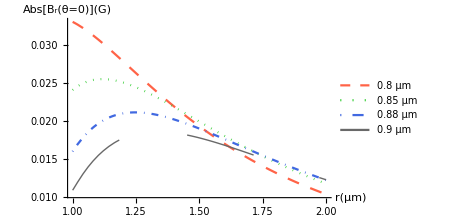

radial9.png

```mathematica
SetDirectory[NotebookDirectory[]]
V=3/299.792458;
c=10^(-4);
r2=1;
r1=0.90;
n=50; (*orden=2n+1*)
a=.;

d3[a_,r_,s_,ϵ_,θ_,l_]:=-l (r^(1+2 l)-s^(1+2 l))((1+l) r^(1+2 l) (-1+ϵ)+a^(1+2 l) (1+l+l ϵ)) θ;
Λ[a_,r_,s_,ϵ_,θ_,l_]:=(V*a^(1+l) )/(-l (1+l) r^(2+4 l) (-1+ϵ)^2+a^(1+2 l) (1+l) (r^(1+2 l)-s^(1+2 l)) (-1+ϵ) (1+l+l ϵ)+r^(1+2 l) s^(1+2 l) (1+l+l ϵ) (l+ϵ+l ϵ));
ψ3[a_,r1_,r_,θ_,n_]:=
Simplify[Sum[(-1/2)^((l-1)/2)(2l+1)(l-2)!!/(2((l+1)/2)!)*Λ[c*a,c*r1,c*r2,4,1/137,l]*(d3[c*a,c*r1,c*r2,4,1/137,l]*(r)^(-l-1))*LegendreP[l,Cos[θ]],{l,1,2*n+1}]-Sum[(-1/2)^((2l-1)/2)(4l+1)(2l-2)!!/(2((2l+1)/2)!)*Λ[c*a,c*r1,c*r2,4,1/137,2l]*(d3[c*a,c*r1,c*r2,4,1/137,2l]*(r)^(-2l-1))*LegendreP[2l,Cos[θ]],{l,1,n}]];

R1[r_]:=ψ3[(r1-0.1),r1,r,0,n];
R2[r_]:=ψ3[(r1-0.05),r1,r,0,n];
R3[r_]:=ψ3[(r1-0.03),r1,r,0,n];
R4[r_]:=ψ3[(r1-0.02),r1,r,0,n];
R5[r_]:=ψ3[(r1-0.01),r1,r,0,n];
R6[r_]:=ψ3[r1,r1,r,0,n];

plot=Show[
Plot[Abs[R1'[c*r]],{r,1,2},PlotLegends->Placed[{r1-0.10} μm ,{0.8,0.9}],PlotRange->All,PlotStyle->{RGBColor[255/255,99/255,71/255],Dashing[0.025]}],
Plot[Abs[R2'[c*r]],{r,1,2},PlotLegends->Placed[{r1-0.05}μm,{0.8,0.8}],PlotRange->All,PlotStyle->{RGBColor[50/255,205/255,50/255],Dotted}],
Plot[Abs[R4'[c*r]],{r,1,2},PlotLegends->Placed[{r1-0.02}μm,{0.8,0.7}],PlotRange->All,PlotStyle->{RGBColor[65/255,105/255,225/255],DotDashed}],
Plot[Abs[R6'[c*r]],{r,1,2},PlotLegends->Placed[{r1}μm,{0.8,0.6}],PlotRange->All,PlotStyle->{RGBColor[105/255,105/255,105/255],Thick,Dashing[10]}],
AxesOrigin->{1,0},PlotRange->All,AxesLabel->{Style["r(μm)",12],Style[Abs[Subscript[B,"r"]["θ=0"]][G],12]},AxesStyle->Black,ImageSize->350
]
Export["radial9.png",plot,ImageResolution->600]
```

C:\Users\DANIEL\Desktop\TESIS\Mathematica

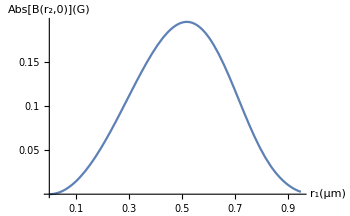

maximize0.png

```mathematica
SetDirectory[NotebookDirectory[]]
V=3/299.792458;
c=10^(-4);
r2=1;
r1=.;
n=100; (*orden=2n+1*)
a=.;

d3[a_,r_,s_,ϵ_,θ_,l_]:=-l (r^(1+2 l)-s^(1+2 l))((1+l) r^(1+2 l) (-1+ϵ)+a^(1+2 l) (1+l+l ϵ)) θ;
Λ[a_,r_,s_,ϵ_,θ_,l_]:=(V*a^(1+l) )/(-l (1+l) r^(2+4 l) (-1+ϵ)^2+a^(1+2 l) (1+l) (r^(1+2 l)-s^(1+2 l)) (-1+ϵ) (1+l+l ϵ)+r^(1+2 l) s^(1+2 l) (1+l+l ϵ) (l+ϵ+l ϵ));
ψ3[a_,r1_,r_,θ_,n_]:=
Simplify[Sum[(-1/2)^((l-1)/2)(2l+1)(l-2)!!/(2((l+1)/2)!)*Λ[c*a,c*r1,c*r2,4,1/137,l]*(d3[c*a,c*r1,c*r2,4,1/137,l]*(r)^(-l-1))*LegendreP[l,Cos[θ]],{l,1,2*n+1}]-Sum[(-1/2)^((2l-1)/2)(4l+1)(2l-2)!!/(2((2l+1)/2)!)*Λ[c*a,c*r1,c*r2,4,1/137,2l]*(d3[c*a,c*r1,c*r2,4,1/137,2l]*(r)^(-2l-1))*LegendreP[2l,Cos[θ]],{l,1,n}]];

max2=Plot[Abs[F'[c*r2]],{r1,0,0.95},AxesLabel->{Style[Subscript[r,1][μm],12],Style[Abs["B" [ Subscript[r,2],"0"]][G],12]},AxesStyle->Black,Ticks->{ticksh,ticksv},ImageSize->350]
Export["maximize0.png",max2,ImageResolution->600]
```

C:\Users\DANIEL\Desktop\SIMPL

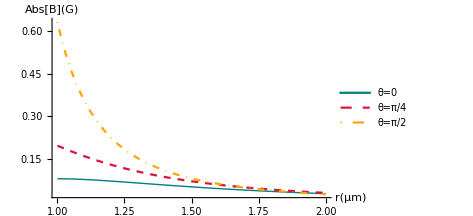

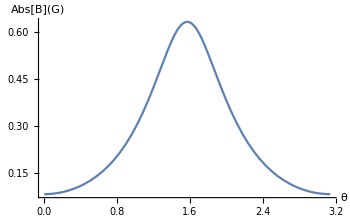

total75_.png

total75_theta.png

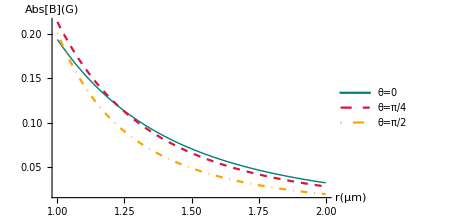

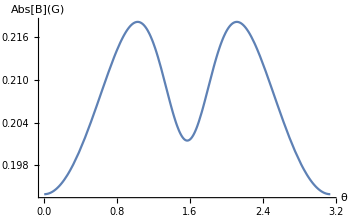

total5_.png

total5_theta.png

```mathematica
SetDirectory[NotebookDirectory[]]
V=3/299.792458;
c=10^(-4);
r2=1;
r1=0.75;
n=15; (*orden=2n+1*)
a=.;
θ=.;


d3[a_,r_,s_,ϵ_,θ_,l_]:=-l (r^(1+2 l)-s^(1+2 l))((1+l) r^(1+2 l) (-1+ϵ)+a^(1+2 l) (1+l+l ϵ)) θ;
Λ[a_,r_,s_,ϵ_,θ_,l_]:=(V*a^(1+l) )/(-l (1+l) r^(2+4 l) (-1+ϵ)^2+a^(1+2 l) (1+l) (r^(1+2 l)-s^(1+2 l)) (-1+ϵ) (1+l+l ϵ)+r^(1+2 l) s^(1+2 l) (1+l+l ϵ) (l+ϵ+l ϵ));
ψ3[a_,r1_,r_,θ_,n_]:=
Simplify[Sum[(-1/2)^((l-1)/2)(2l+1)(l-2)!!/(2((l+1)/2)!)*Λ[c*a,c*r1,c*r2,4,1/137,l]*(d3[c*a,c*r1,c*r2,4,1/137,l]*(r)^(-l-1))*LegendreP[l,Cos[θ]],{l,1,2*n+1}]-Sum[(-1/2)^((2l-1)/2)(4l+1)(2l-2)!!/(2((2l+1)/2)!)*Λ[c*a,c*r1,c*r2,4,1/137,2l]*(d3[c*a,c*r1,c*r2,4,1/137,2l]*(r)^(-2l-1))*LegendreP[2l,Cos[θ]],{l,1,n}]];

R[r_,θ_]:=Simplify[D[ψ3[r1,r1,r,θ,n],r]];
Θ[r_,θ_]:=Simplify[1/r*D[ψ3[r1,r1,r,θ,n],θ]];
B[r_,θ_]:=;
Sqrt[(R[r,θ])^2+(Θ[r,θ])^2];


plt1=Show[
Plot[B[c*x,0],{x,1,2},PlotLegends->Placed[{"θ=0"},{0.8,0.9}],PlotRange->All,PlotStyle->{RGBColor[0,128/255,128/255],Thick}],
Plot[B[c*x,Pi/4],{x,1,2},PlotLegends->Placed[{"θ=π/4"},{0.8,0.8}],PlotRange->All,PlotStyle->{RGBColor[220/255,20/255,60/255],Dashed}],
Plot[B[c*x,Pi/2],{x,1,2},PlotLegends->Placed[{"θ=π/2"},{0.8,0.7}],PlotRange->All,PlotStyle->{RGBColor[1,165/255,0],DotDashed}], AxesOrigin->{Automatic,0},PlotRange->All,AxesLabel->{Style["r(μm)",12],Style[Abs[B][G],12]},AxesStyle->Black,ImageSize->350]

plt2=Plot[B[c*r2,θ],{θ,0,Pi},PlotRange->All,AxesLabel->{Style["θ",12],Style[Abs[B][G],12]},AxesOrigin->{Automatic,0.0},AxesStyle->Black,ImageSize->350]
Export["total75_.png",plt1,ImageResolution->600]
Export["total75_theta.png",plt2,ImageResolution->600]
```

C:\Users\DANIEL\Desktop\Physics\TESIS\Avances\CORRECCION

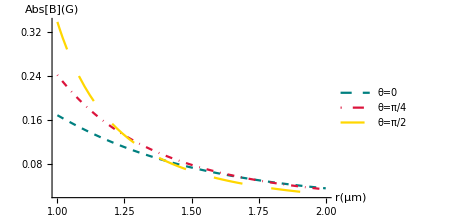

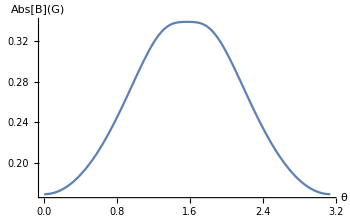

total62_.png

total62_theta.png

```mathematica
V=3/299.792458;
c=10^(-4);
r2=1;
r1=0.5;
n=15; (*orden=2n+1*)
a=.;
θ=.;
SetDirectory[NotebookDirectory[]]
d3[a_,r_,s_,ϵ_,θ_,l_]:=-l (r^(1+2 l)-s^(1+2 l))((1+l) r^(1+2 l) (-1+ϵ)+a^(1+2 l) (1+l+l ϵ)) θ;
Λ[a_,r_,s_,ϵ_,θ_,l_]:=(V*a^(1+l) )/(-l (1+l) r^(2+4 l) (-1+ϵ)^2+a^(1+2 l) (1+l) (r^(1+2 l)-s^(1+2 l)) (-1+ϵ) (1+l+l ϵ)+r^(1+2 l) s^(1+2 l) (1+l+l ϵ) (l+ϵ+l ϵ));
ψ3[a_,r1_,r_,θ_,n_]:=
Simplify[Sum[(-1/2)^((l-1)/2)(2l+1)(l-2)!!/(2((l+1)/2)!)*Λ[c*a,c*r1,c*r2,4,1/137,l]*(d3[c*a,c*r1,c*r2,4,1/137,l]*(r)^(-l-1))*LegendreP[l,Cos[θ]],{l,1,2*n+1}]-Sum[(-1/2)^((2l-1)/2)(4l+1)(2l-2)!!/(2((2l+1)/2)!)*Λ[c*a,c*r1,c*r2,4,1/137,2l]*(d3[c*a,c*r1,c*r2,4,1/137,2l]*(r)^(-2l-1))*LegendreP[2l,Cos[θ]],{l,1,n}]];
Evaluate[Simplify[D[ψ3[r1,r1,r,θ,n],r]]]
Simplify[1/r*D[ψ3[r1,r1,r,θ,n],θ]]
R[r_,θ_]:=;
Θ[r_,θ_]:=;
```

C:\Users\DANIEL\Desktop\SIMPL

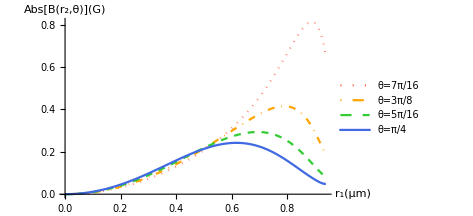

plots1.png

```mathematica
SetDirectory[NotebookDirectory[]]

V=.;
c=10^4;
r1=.;
α=1/137;
ϵ=4;

a=.;
n=30;

V[l_]:=3/299.792458*(-1/2)^((l-1)/2)(2*l+1)(l-2)!!/(2((l+1)/2)!);
d3[a_,l_]:=-α*l* ϵ(a^(2l+1)-1)*a^(l+1)*V[l]/((l+1)*(ϵ-1)*a^(2l+1)+(l*ϵ+l+1));

ψ3[a_,r_,θ_,n_]:=Sum[d3[a,2*l+1]*r^(-2l-2)*LegendreP[2*l+1,Cos[θ]],{l,0,n}];

ρθ[θ_]:=ψ3[a,1,θ,n];
ρr[r_]:=ψ3[a,r,Pi/4,n];
ηθ[θ_]:=ψ3[a,1,θ,n];
ηr[r_]:=ψ3[a,r,5*Pi/16,n];
σθ[θ_]:=ψ3[a,1,θ,n];
σr[r_]:=ψ3[a,r,6*Pi/16,n];
χθ[θ_]:=ψ3[a,1,θ,n];
χr[r_]:=ψ3[a,r,7*Pi/16,n];

yes=Show[
Plot[Sqrt[(c*χθ'[7*Pi/16])^2+(c*χr'[1])^2],{a,0,0.94},PlotLegends->Placed[{"θ=7π/16"},{0.25,0.65}],PlotRange->All,PlotStyle->{RGBColor[255/255,99/255,71/255],Dotted}],
Plot[Sqrt[(c*σθ'[3*Pi/8])^2+(c*σr'[1])^2],{a,0,0.94},PlotLegends->Placed[{"θ=3π/8"} ,{0.25,0.75}],PlotRange->All,PlotStyle->{RGBColor[1,165/255,0],DotDashed}],
Plot[Sqrt[(c*ηθ'[5*Pi/16])^2+(c*ηr'[1])^2],{a,0,0.94},PlotLegends->Placed[{"θ=5π/16"} ,{0.25,0.85}],PlotRange->All,PlotStyle->{RGBColor[50/255,205/255,50/255],Dashed}],
Plot[Sqrt[(c*ρθ'[Pi/4])^2+(c*ρr'[1])^2],{a,0,0.94},PlotLegends->Placed[{"θ=π/4"} ,{0.25,0.95}],PlotRange->All,PlotStyle->{RGBColor[65/255,105/255,225/255]}],
AxesLabel->{Style[Subscript[r,1][μm],12],Style[Abs["B"[ Subscript[r,2],θ]][G],12]},AxesStyle->Black,ImageSize->350]
Export["plots1.png",yes,ImageResolution->600]
```